```mathematica
CloudPublish[EvaluationNotebook[],"QuantumChannelTicTacToe.nb"]
```

CloudObject[https://www.wolframcloud.com/obj/nikm/QuantumChannelTicTacToe.nb]

```mathematica
FoldGraph // ClearAll
FoldGraph[f_, init_List, l_List, opts : OptionsPattern[Graph]] := Graph[
	Catenate @ Rest @ FoldList[
		{xs, y} |-> Catenate @ Map[
			x |-> If[MatchQ[#, _ -> _], DirectedEdge[x, #[[2]], #[[1]]], DirectedEdge[x, #]] & /@ Developer`ToList[f[x, y]],
			DeleteDuplicates @ If[MatchQ[xs, {___DirectedEdge}], xs[[All, 2]], xs]
		],
		init,
		l
	],
	opts
]
```

```mathematica
(*operatorApply[op_, states_] := With[{
	order = op["InputOrder"]
},
	MapAt[ReplacePart[states, Thread[order -> #]] &, op["State"][QuantumTensorProduct @@ states[[order]]]["DecomposeWithProbabilities"], {All, 2}]
]*)

operatorApply[op_, states_] := With[{
	order = op["InputOrder"]
},
	Map[With[{n = Length[#] - Length[order]}, Join[ReplacePart[states, Thread[order -> Drop[#, n]]], Take[#, n]]] &, op["State"][QuantumTensorProduct @@ states[[order]]]["Decompose"]]
]
```

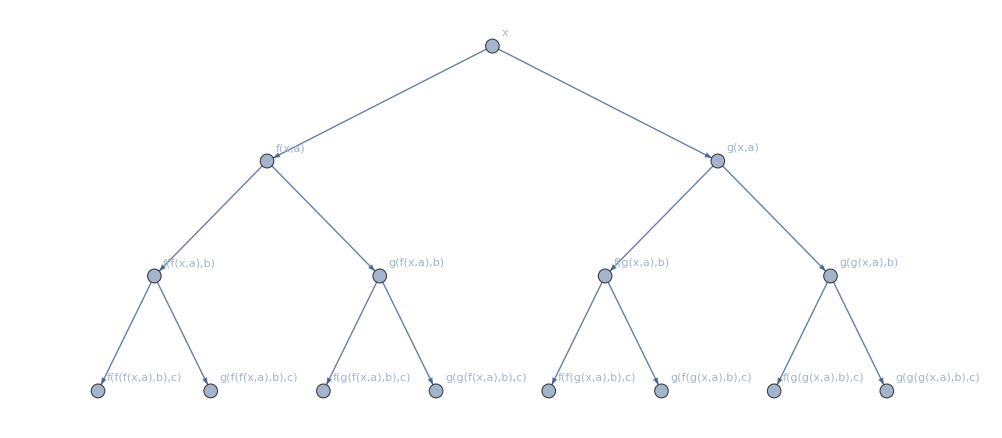

```mathematica
FoldGraph[{f[#1,#2],g[#1,#2]}&,{x},{a,b,c},VertexLabels->Automatic]
```

```mathematica
CircuitMultiwayGraph[circuit_, initStates_ : Automatic] := FoldGraph[
	{s, op} |-> Map[{s[[1]] + 1, #} &] @ operatorApply[op, s[[2]]],
	{{0, Replace[initStates, Automatic -> Table[QuantumState["0"], circuit["Arity"]]]}},
	circuit["Operators"],
	GraphLayout -> "LayeredDigraphEmbedding"
]
```

Define 0,1 and 2 (3D qudit)

```mathematica
qudits=QuantumState[#,3]&/@Permutations[PadRight[{1},3]];
```

non-unitary to transform 0->1

```mathematica
u1=QuantumOperator[qudits[[2]][qudits[[1]]["Dagger"]]]
```

QuantumOperator[…]

channel corresponding to player 1. It looks into all cells, and marks all 0 by 1

```mathematica
player1=QuantumChannel[Table[QuantumOperator[u1,{i}],{i,4}]];
```

```mathematica
player1["State"][QuantumTensorProduct[Table[N@QuantumState[{1},3],4]]]["Decompose"]
```

non-unitary to transform 0->2

```mathematica
u2=QuantumOperator[qudits[[3]][qudits[[1]]["Dagger"]]]
```

QuantumOperator[…]

channel corresponding to player 1 (look into all cells, and mark all 0 by 2)

```mathematica
player2=QuantumChannel[Table[QuantumOperator[u2,{i}],{i,4}]];
```

```mathematica
QuantumCircuitOperator[{QuantumCircuitOperator[player1,"p1"],QuantumCircuitOperator[player2,"p2"],QuantumCircuitOperator[player1,"p1"],QuantumCircuitOperator[player2,"p2"]}]
```

-Graphics-

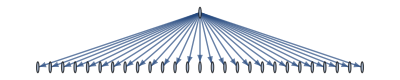

```mathematica
CircuitMultiwayGraph[QuantumCircuitOperator[QuantumOperator[{"RandomUnitary",3},Range[4]]],Table[N@QuantumState[{1},3],4]]
```

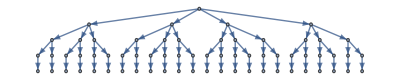

```mathematica
cmwg=CircuitMultiwayGraph[QuantumCircuitOperator[player1]/*QuantumCircuitOperator[player2]/*QuantumCircuitOperator[player1]/*QuantumCircuitOperator[player2],Table[N@QuantumState[{1},3],4]]
```

```mathematica
SimpleGraph@VertexReplace[cmwg,v_:>Normal@MapAt[#["Computational"]["CanonicalStateVector"]&,v,{2,All}][[2,;;4]],VertexShapeFunction->
Function[Inset[ResourceFunction["CharacterArrayPlot"][ArrayReshape[Position[#,1.]&/@#2,{2,2}],"CharacterStyleRules"->{x_:>{8,Black,Bold}},"CharacterRules"->{1->"",2->"X",3->"O"},
ColorRules->{1->White,2->Lighter[Orange,.5],3->Lighter[Purple,.7]},
MeshStyle->Directive[Thick,LightGray],
Frame->False,FrameTicks->False,
FrameStyle->Directive[Blend[{Orange,Red},.3],Thickness[.05]],
ImageSize->20],#1,#3]],
PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
IsomorphicGraphQ[%,{{"[◼]", "TTTGraph"}}[2,{{{{0,0},{0,0}},1}},AspectRatio->1/2,VertexSize->.6]]
```

True